# The Particle in a Box

Now that we have gone through the postulates of quantum mechanics, we have our first chance to apply everything that we have learned so far to evaluate a model system.

## Purpose

The purpose of this lesson is to...

demonstrate the application of the postulates of quantum mechanics to the analysis of a model system, the particle in a box.

reveal some general attributes of quantum mechanical systems that arise from finding the solutions of the time-independent Schrödinger equation.

present an example of how even a simplified model like the particle in a box can be applied to interpret experimental results.

## Learning Objectives

At the end of this lesson, I should be able to...

solve for and interpret the meaning of the wavefunction in a model system.

explain the origin of quantization in quantum mechanical systems.

evaluate the expectation value of operators for a wavefunction.

describe the connection between quantized states in a model system and quantized states in a molecule.

## Solving the Schrödinger Equation for a Particle in a Box

It turns out that there are only a few relevant problems for which the Schrödinger equation can be solved exactly (meaning we can write out an answer by working through some calculus and algebra). For more complex systems, we have to resort to numerical methods.  Nevertheless, working through these problems helps us illustrate many central concepts that are also relevant for more complex systems.

### The Particle in a One-Dimensional Box

The problem of a particle in a one-dimensional “box” (which is actually a line) involves a particle of mass m that is constrained to the x-axis between x = 0 and x = a. We say that the particle is “free” in this region, meaning that it experiences no potential energy. We communicate this statement mathematically by writing that V (x ) = 0 between x = 0 and x = a. To make sure the particle is in fact constrained, we state that the potential energy outside of this region is infinite, so V (x ) = ∞. We can visualize the potential energy as shown below:

V(x)=Piecewise[{{0, 0≤x≤a}, {∞, otherwise}}]

```mathematica
pw=Piecewise[{{0,0≤x≤1}},1]
Plot[pw,{x,-1,3},PlotRange->{{-0.5,1.5},{-0.1,0.9}},BaseStyle->{FontFamily->"Arial",FontSize->16},PlotStyle->Directive[Black,PointSize[Large]],AxesStyle->Directive[Thick,Black],TicksStyle->Directive[Black, Thick],Ticks->{{{-0.5,"-L"},{0,"0"},{1,"a"}},{{1,"a"}}},ImageSize->Medium, Exclusions->None,AxesOrigin->{-0.5,0},AxesLabel->{"x","V(x)"},Filling->0,FillingStyle->HatchFilling[-Pi/4]]
```

Piecewise[{{0, 0≤x≤1}, {1, True}}]

-Graphics-

Figure 4.1. Visualization of the potential V(x) for a particle constrained to move on a line between x = 0 and x = a.

We want to solve the time-independent Schrödinger equation (TISE) for this system. Remember that the TISE is written

-ℏ^2/(2m)(ⅆ^2 ψ(x))/(ⅆ x^2)+V(x)ψ(x)=E ψ(x)

Using the potential V (x ) defined above, we can write the TISE within the box as

-ℏ^2/(2m)(ⅆ^2 ψ(x))/(ⅆ x^2)=E ψ(x)          0≤x≤a

Because we have defined the potential to be infinite on either side of the box, we can use similar constraints to those we used on a fixed, vibrating string. That is, we can say that ψ(x ) must be zero at the two ends of the box:

ψ(0)=ψ(a)=0

### Solving the Schrödinger Equation

Now we have the TISE that describes the particle, and we have some boundary conditions. We can combine these two pieces of information to try to find the solution to the Schrödinger equation, meaning we solve for ψ(x ). If we rearrange equation (3) slightly, we get the equation

(ⅆ^2 ψ(x))/(ⅆ x^2)+(2mE)/ℏ^2 ψ(x)=0          0≤x≤a

equation (5) is of the same form as the position-dependent portion of the classical wave equation we solved in lesson 02,

(ⅆ^2 X(x))/(ⅆ x^2)+k^2 X(x)=0

recall that in that lesson, we found that the solutions took the form

X(x)=c_1 cos(kx)+c_2 sin(kx)

where c_1 and c_2 are constants. Applying that knowledge here, we can say that the solutions will take the form

ψ(x)=c_1 cos(kx)+c_2 sin(kx)

where

k=(√(2mE))/ℏ

Plugging in our first boundary condition, ψ(0) = 0, we find

ψ(0)=c_1 cos(0)+c_2 sin(0)=0

Remembering that cos(0) = 1 and sin(0) = 0, we obtain

c_1=0

Now, plugging in our second boundary condition, ψ(a ) = 0, we find

ψ(a)=c_2 sin(ka)=0

since c_2 = 0 would give us no wave, we choose that

sin(ka)=0

to fulfill this condition, we must have

ka=(√(2mE))/ℏ a=nπ          n = 1,2,3...

solving equation (14) for E, which we will now call E_n to denote that it depends on the value of n, we find

E_n=(n^2 π^2 ℏ^2)/(2 ma^2)

recalling that ℏ = h/2π, we can simplify a bit to obtain

E_n=(n^2 h^2)/(8 ma^2)

We’ll come back to the implications of equation (16) in a moment, but we still haven’t finished solving for ψ(x ). Up to this point, we have found that

ψ_n(x)=c_2 sin(kx)

where we are now noting that there is a different wavefunction for each value of n. Substituting equation (14) into equation (17), we find that

ψ_n(x)=c_2 sin(nπx/a)

To solve for c_2, we’ll have to use another one of our postulates of quantum mechanics.

### Normalizing the Wavefunction

We don’t have any more boundary conditions to help us constrain the value of c_2, but we do have another condition that we can apply. Remember that, since we have a probabilistic interpretation of the wavefunction, the wavefunction must obey the condition

∫_(-∞)^∞ ψ^⋆(x)ψ(x)dx=1

Or, in this case, since the wavefunction must be zero outside of the interval from 0 to a,

∫_0^a ψ^⋆(x)ψ(x)dx=1

Substitute equation (18) for ψ( x ) in equation (20), we obtain

|^c_2|^2∫_0^a sin^2(nπx/a)dx=1

The simplest way to solve the integral is to use a substitution of variables,

z=nπx/a

and

a/nπ ⅆz=ⅆx

Substituting into equation (21) gives us

(|c_2|)^2(a/nπ)∫_0^nπ sin^2(z)dz=(|c_2|)^2(a/nπ)(nπ/2)=1

We can now solve for c_2 and find that

c_2=(2/a)^(1/2)

The final, normalized wavefunctions are then given by

ψ_n(x)=(2/a)^(1/2)sin(nπx/a)

Below is a plot of the wavefunctions, ψ_n, for n = 1 through 4, with each wavefunction plotted with an offset of E_n for the corresponding value of n. Note that the scale of the wavefunctions (i.e., the correct amplitude) is not shown, but you can see the shape and location of maxima and nodes. These are the same types of solutions as we saw for the vibrating string.

```mathematica
a=1;
h=1;
m=1;
energies=
Table[(n^2*h^2)/(8*m*a^2),{n,1,4}];
energiesplot=
Table[{{0,energies[[n]]},{a,energies[[n]]}},{n,1,4}];
potential=Piecewise[{{0,0≤x≤1}},1000];
wf=Table[0.1*(2/a)^(1/2)Sin[n*Pi*x/a]+energies[[n]],{n,1,4}];
Show[
Plot[potential,{x,-1,3},PlotRange->{{-0.2,1.2},{-0.1,2.5}},BaseStyle->{FontFamily->"Arial",FontSize->16},PlotStyle->Directive[Black,PointSize[Large]],AxesStyle->Directive[Thick,Black],TicksStyle->Directive[Black, Thick],Ticks->{{{-0.5,"-L"},{0,"0"},{1,"a"}},Table[{energies[[n]],Subscript["E",ToString[n]]},{n,1,4}]},ImageSize->Large, Exclusions->None,AxesOrigin->{-0.2,0},AxesLabel->{"x","E"},Filling->0,FillingStyle->HatchFilling[-Pi/4]]
,
ListLinePlot[energiesplot[[1;;4]],PlotStyle->Directive[Black]]
,
Plot[wf[[1;;4]],{x,0,1},PlotRange->All,PlotStyle->Thick]
]
```

-Graphics-

Figure 4.2. Plot of the eigenfunctions ψ_n(x)=(2/a)^(1/2)sin(nπx/a) for values of n from 1 (bottom) to 4 (top), offset by the associated energies E_n.

And here is a similar plot, this time showing  |ψ_n(x)|^2, which, remember, tells you the probability of finding the particle at a given location.

```mathematica
a=1;
h=1;
m=1;
energies=
Table[(n^2*h^2)/(8*m*a^2),{n,1,4}];
energiesplot=
Table[{{0,energies[[n]]},{a,energies[[n]]}},{n,1,4}];
potential=Piecewise[{{0,0≤x≤1}},1000];
wfsquared=Table[0.1*((2/a)^(1/2)Sin[n*Pi*x/a])^2+energies[[n]],{n,1,4}];
Show[
Plot[potential,{x,-1,3},PlotRange->{{-0.2,1.2},{-0.1,2.5}},BaseStyle->{FontFamily->"Arial",FontSize->16},PlotStyle->Directive[Black,PointSize[Large]],AxesStyle->Directive[Thick,Black],TicksStyle->Directive[Black, Thick],Ticks->{{{-0.5,"-L"},{0,"0"},{1,"a"}},Table[{energies[[n]],Subscript["E",ToString[n]]},{n,1,4}]},ImageSize->Large, Exclusions->None,AxesOrigin->{-0.2,0},AxesLabel->{"x","E"},Filling->0,FillingStyle->HatchFilling[-Pi/4]]
,
ListLinePlot[energiesplot[[1;;4]],PlotStyle->Directive[Black]]
,
Plot[wfsquared[[1;;4]],{x,0,1},PlotRange->All,PlotStyle->Thick]
]
```

-Graphics-

Figure 4.3. Plot of the square of the eigenfunctions |ψ_n(x)|^2 of the particle in a box for values of n from 1 (bottom) to 4 (top), offset by the associated energies E_n.

## Interpreting the Solutions for a Particle in a Box

### The Energy of a Particle in a Box is Quantized

We saw above that the energy values for a particle in a box are given by

E_n=(n^2 π^2 ℏ^2)/(2 ma^2)

meaning that the energy only has discrete values and no other values. Simply as a result of imposing boundary conditions, we have constrained the energy of the particle. When we encounter equations like this in quantum mechanics, we often refer to n as a quantum number. In lesson 01, we noted that Planck had asserted that energy must be quantized in integer values to explain blackbody radiation. We now know that the quantization of energy levels is a direct result of finding solutions to the time-independent Schrödinger equation, and these numbers don’t have to be inserted without explanation.

### The Lowest-Energy State doesn’t have an Energy of Zero

If we solve the equation for the allowed energy levels for n = 1, we find that

E_1=(π^2 ℏ^2)/(2 ma^2)

In other words, the lowest allowed energy state of a particle in a box is not equal to zero. For quantum mechanical systems, the energy of this lowest, or ground, state is typically called the zero-point energy. It is, again, a natural consequence of finding the solutions of the TISE, but it is also consistent with the Heisenberg uncertainty principle, because an energy of zero would imply that the particle’s position and momentum are both known exactly.

### The Absolute Square of the Wavefunction gives us Location Probability

Since we have properly normalized our wavefunction, we can now say that the probability that an object in the state specified by ψ_n(x )  will be found in the volume element dx located at x is given by

ψ^⋆(x)ψ(x)dx

in accordance with the first postulate of quantum mechanics.

In other words, we can calculate the probability of finding the particle in the interval x_1≤x≤x_2 as

∫_x_1^x_2 ψ^⋆(x)ψ(x)dx

Looking at the graphs of  |ψ_n(x)|^2 again,

```mathematica
a=1;
h=1;
m=1;
energies=
Table[(n^2*h^2)/(8*m*a^2),{n,1,4}];
energiesplot=
Table[{{0,energies[[n]]},{a,energies[[n]]}},{n,1,4}];
potential=Piecewise[{{0,0≤x≤1}},1000];
wfsquared=Table[0.1*((2/a)^(1/2)Sin[n*Pi*x/a])^2+energies[[n]],{n,1,4}];
Show[
Plot[potential,{x,-1,3},PlotRange->{{-0.2,1.2},{-0.1,2.5}},BaseStyle->{FontFamily->"Arial",FontSize->16},PlotStyle->Directive[Black,PointSize[Large]],AxesStyle->Directive[Thick,Black],TicksStyle->Directive[Black, Thick],Ticks->{{{-0.5,"-L"},{0,"0"},{1,"a"}},Table[{energies[[n]],Subscript["E",ToString[n]]},{n,1,4}]},ImageSize->Large, Exclusions->None,AxesOrigin->{-0.2,0},AxesLabel->{"x","E"},Filling->0,FillingStyle->HatchFilling[-Pi/4]]
,
ListLinePlot[energiesplot[[1;;4]],PlotStyle->Directive[Black]]
,
Plot[wfsquared[[1;;4]],{x,0,1},PlotRange->All,PlotStyle->Thick]
]
```

-Graphics-

Figure 4.4. Plot of the square of the eigenfunctions |ψ_n(x)|^2 of the particle in a box for values of n from 1 (bottom) to 4 (top), offset by the associated energies E_n.

we can see that the most probable position for the lowest-energy state is in the middle of the box, but the higher-energy levels have multiple peaks in the probability distribution, most of which are not at x = (1/2)a.

### We Obtain the Average Value of an Observable through an Expectation Value

Recall that the fourth postulate tells us that the average value of the observable corresponding to a given quantum mechanical operator Â is given by

<A> =∫_(-∞)^∞ ψ^⋆(x)Â ψ(x)dx

let’s try calculating the average value of x, <x>

<x> =∫_(-∞)^∞ ψ^⋆(x)X̂ ψ(x)dx

=∫_0^a ψ^⋆(x)x ψ(x)dx

=∫_0^a (2/a)^(1/2)sin(nπx/a)x(2/a)^(1/2)sin(nπx/a)dx

=(2/a)∫_0^a x sin^2(nπx/a)dx

=(2/a)(a^2/4)=a/2

Note that this value does not depend on n, so the average value of the position is always in the center of the box. This result makes sense because all of the eigenfunctions are symmetric.

If we carry out a similar result for the momentum p using the momentum operator

P̂=-ⅈℏ d/dx

Substituting in equation (31), we obtain

<p> =∫_(-∞)^∞ ψ^⋆(x)P̂ ψ(x)dx

=∫_0^a ψ^⋆(x)-ⅈℏⅆ/ⅆx ψ(x)dx

=∫_0^a (2/a)^(1/2)sin(nπx/a)-ⅈℏ ⅆ/ⅆx(2/a)^(1/2)sin(nπx/a)dx

=(2/a)∫_0^a sin(nπx/a)-ⅈℏ nπ/a cos(nπx/a)dx

=-ⅈℏ((2nπ)/a^2)∫_0^a sin(nπx/a) cos(nπx/a)dx

Because

∫_0^a sin(nπx/a) cos(nπx/a)dx = 0

the average value of the momentum is also zero,

<p> = 0

Conceptually, thinking about the momentum as telling us about which direction the particle is moving, we can say that the particle is equally likely to be moving in either direction.

### Variance and the Uncertainty Principle

In lesson 03, we discussed the Heisenberg uncertainty principle in terms of the standard deviation of momentum and position,

ΔxΔp≥ℏ/2

or, more formally,

σ_x σ_p≥ℏ/2

In that lesson, we discussed the standard deviation in the form of its statistical definition for a number of measurements. However, the standard deviation can also be defined in terms of expectation values. For a variable x, the variance (square of the standard deviation) can be written as

σ_x^2=⟨x^2⟩-⟨x⟩^2

In other words, it’s the mean square minus the square of the mean. We can validate the Heisenberg uncertainty principle for the particle in a box using this formulation.

## Application of the Particle in a Box

We have thus far used the model of a particle in a box to illustrate how we can apply the postulates of quantum mechanics to interpret systems described by the Schrödinger equation. However, we can apply it as a simplistic model to interpret the properties of certain molecules. Specifically, the particle-in-a-box system can act as a model for the π electrons in linear conjugated hydrocarbons.

Let’s take the example of butadiene,

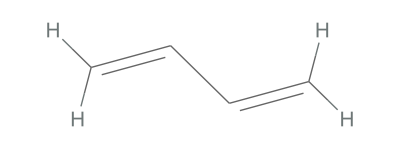

-Graphics3D-

```mathematica
m=Molecule["Butadiene"];
MoleculePlot[m]
MoleculePlot3D[m,PlotTheme->"BallAndStick"]
```

Figure 8.3. Butadiene in skeletal formula (top) and ball-and-stick model (bottom).

Although clearly not a linear molecule, let’s make the approximation that the π electrons in butadiene move along a straight line, whose length we can estimate as 578 pm (two C=C bonds plus one C-C bond plus two carbon atom radii). This molecule has four π electrons, but we can actually put two in each energy level according the to Pauli exclusion principle. Recalling that the energies are given by

E_n=(n^2 π^2 ℏ^2)/(2 ma^2)

we want to find the energy difference between the lowest unoccupied state (E_3) and the highest occupied state (E_2). Plugging in the values into our equation, we find

E_3-E_2=(π^2 ℏ^2)/(2 ma^2)(3^2-2^2)

=h^2/(8 ma^2)(3^2-2^2)

=((6.626 × 10^-34 J s)^2)/(8(9.109 × 10^-31 kg)(578 × 10^-12 m)^2)(3^2-2^2)

Letting Mathematica help us out,

```mathematica
((6.626*^-34)^2/(8*9.109*^-31*(578*^-12)^2))*(3^2-2^2)
```

9.01688×10^-19

E_3-E_2=9.02×10^-19 J

That’s not really a convenient unit to work with, so we convert it to wavenumbers using

ν̃=ΔE/hc =(9.02×10^-19 J)/((6.626 × 10^-34 J s)(2.998 × 10^8 m s^-1))=4.54 × 10^6 m^-1=4.54 × 10^4 cm^-1

The actual experimental value is roughly 4.61× 10^4 cm^-1, so the approximation is not too far off (although not good enough for spectroscopic prediction). Below is an experimental measurement of direct absorption of trans-1,3-butadiene in the expected transition range:

Figure 4.4. Direct absorption spectrum of trans-1,3-butadiene. From Leopold, D. G.; Pendley, R. D.; Roebber, J. L.; Hemley, R. J.; Vaida, V., Direct absorption spectroscopy of jet-cooled polyenes. II. The 1^1 B_u^+ ← 1^1 A_g^- transitions of butadienes and hexatrienes. J. Chem. Phys. 1984, 81 (10), 4218-4229.

To understand why there are multiple features here instead of just one, we have to discuss a great deal more about molecular spectroscopy. Also, this paper was published in 1984, but people were still trying to accurately predict the spectrum in 2019 (the red in the figure below is the predicted spectrum):

Figure 4.5. Experimental (black) and predicted (red) direct absorption spectrum of trans-1,3-butadiene. From Rabidoux, S. M.; Cave, R. J.; Stanton, J. F., Nonadiabatic Investigation of the Electronic Spectroscopy of trans-1,3-Butadiene. J. Phys. Chem. A 2019, 123 (15), 3255-3271.

## A Particle in a Three-Dimensional Box

Now let’s quickly take a look at what happens when we have a particle in a three-dimensional box (rather than just on a line that we are calling a box). Recall that the three-dimensional time-independent Schrödinger equation is written

-ℏ^2/(2m)∇^2 ψ(r)+V(r)ψ(r)=E ψ(r)

where the Laplacian operator ∇^2  is given by

∇^2 f=∇·∇f=(∂^2 f)/(∂x^2)+(∂^2 f)/(∂y^2)+(∂^2 f)/(∂z^2)

We will call the lengths of the three sides of the box a, b, and c in dimensions x, y, and z, respectively. The potential function is then

V(x,y,z)=Piecewise[{{0, 0≤x≤a,0≤y≤b ,0≤z≤c}, {∞, otherwise}}]

The TISE is then written

-ℏ^2/(2m)∇^2 ψ(r)=E ψ(r)

inside of the box. If we use separation of variables again, we can write our wavefunction as

ψ(x,y,z)=X(x)Y(y)Z(z)

without going through all of the math (which you have already done many times at this point), we find that we can write the TISE as

-ℏ^2/(2m)1/(X(x))(d^2 X(x))/dx^2-ℏ^2/(2m)1/(Y(y))(d^2 Y(y))/dy^2-ℏ^2/(2m)1/(Z(Z))(d^2 Z(z))/dz^2=E

We can readily separate this into three equations by using

E=E_x+E_y+E_z

to get

-ℏ^2/(2m)1/(X(x))(d^2 X(x))/dx^2=E_x

-ℏ^2/(2m)1/(Y(y))(d^2 Y(y))/dy^2=E_y

-ℏ^2/(2m)1/(Z(Z))(d^2 Z(z))/dz^2=E_z

By this point, I’m guessing the math is becoming familiar to you. We will end up with solutions to each of these equations that look the same as our solutions in one dimension, subject to dimension-specific quantum numbers n_x,n_y, and n_z.

A conceptually more important point is made by this example, however. Notice that we were able to write our TISE as a sum of parts.

Ĥ ψ(x,y,z)=E ψ(x,y,z)

was written as

(OverHat[H_x]+OverHat[H_y]+OverHat[H_z])ψ(x,y,z)=(E_x+E_y+E_z) ψ(x,y,z)

where

OverHat[H_x]=-ℏ^2/(2m)∂^2/(∂x^2)

OverHat[H_y]=-ℏ^2/(2m)∂^2/(∂y^2)

OverHat[H_z]=-ℏ^2/(2m)∂^2/(∂z^2)

when we have such a separable Hamiltonian, we can find the final eigenfunctions as the product of the eigenfunctions for each part of the Hamiltonian, as in the separation of variables

ψ(x,y,z)=X(x)Y(y)Z(z)

In addition, the energies of the system are just the sum of the eigenvalues for each part of the Hamiltonian,

E=E_x+E_y+E_z

In this way, we can reduce complicated problems in quantum mechanics (such as the many components of the energy of a molecule) to several simpler problems.